```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/chi-q_dist/num"]
```

/Users/yuichirotada/Documents/Univ/chi-q_dist/num

```mathematica
0.1^(-1/3)
```

2.15443

```mathematica
1/2 Erfc[24/Sqrt[2]]//N
```

1.39039×10^-127

```mathematica
FindRoot[1/2 Erfc[νth/Sqrt[2]]==7.2 10^-16,{νth,10}]
```

{νth→7.98198}

```mathematica
1/2 Erfc[8/Sqrt[2]]//N
```

6.22096×10^-16

```mathematica
FindRoot[1/2 Erfc[νth/Sqrt[2]]==10^-3 7.2 10^-16(10^34/10^20)^(-1/2),{νth,10}]
```

{νth→10.4516}

```mathematica
1/2 Erfc[11/Sqrt[2]]//N
10^-3 7.2 10^-16((6 10^34)/10^20)^(-1/2)
```

1.91066×10^-28

2.93939×10^-26

```mathematica
$Assumptions={β>0,KK>0,MH>0,M>0,calM>0,q>0,a2>0,M1>0,M2>0};
```

```mathematica
params={β->0.36,KK->3.3,σ0->0.08,νth->24,γ->0.85,MH->1};
```

```mathematica
xpcoord={a1,a2,ν1,ν2,c1,c2,ϕ1,ϕ2};
n=8;
```

```mathematica
MPBH[ν_]=KK MH(ν σ0-νth σ0)^β;
νPBH[M_]=(M/(KK MH))^(1/β)/σ0+νth;
```

```mathematica
MPBH[νPBH[M]]//Simplify
```

M

```mathematica
xcoordinxp={a1,a2,MPBH[ν1],MPBH[ν2],c1,c2,ϕ1,ϕ2};
Jxxp=Table[D[xcoordinxp[[j]], xpcoord[[i]]],{i,n},{j,n}]//Simplify
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,KK MH β σ0 ((ν1-νth) σ0)^(-1+β),0,0,0,0,0},{0,0,0,KK MH β σ0 ((ν2-νth) σ0)^(-1+β),0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Det[Jxxp]//Simplify
Det[Jxxp]/.{ν1->νPBH[M1],ν2->νPBH[M2]}//Simplify
```

KK^2 MH^2 β^2 σ0^2 ((ν1-νth) σ0)^(-1+β) ((ν2-νth) σ0)^(-1+β)

M1 M2 ((M1 M2)/(KK^2 MH^2))^(-1/β) β^2 σ0^2

```mathematica
charpM[M1_,M2_]=(M1 M2)^(3/5)/(M1+M2)^(1/5);
ratioq[M1_,M2_]=M2/M1;
χeff[a1_,a2_,q_,c1_,c2_]=(a1 c1+q a2 c2)/(1+q);
M1Mq[calMM_,qq_]=MM1/.Solve[charpM[MM1,MM2]==calMM&&ratioq[MM1,MM2]==qq,{MM1,MM2}][[1]]
M2Mq[calMM_,qq_]=MM2/.Solve[charpM[MM1,MM2]==calMM&&ratioq[MM1,MM2]==qq,{MM1,MM2}][[1]]
```

(calMM (1+qq)^(1/5))/qq^(3/5)

calMM qq^(2/5) (1+qq)^(1/5)

```mathematica
charpM[M1Mq[calM,q],M2Mq[calM,q]]//Simplify
ratioq[M1Mq[calM,q],M2Mq[calM,q]]//Simplify
```

calM

q

```mathematica
xcoord={a1,a2,M1,M2,c1,c2,ϕ1,ϕ2};
ycoord={charpM[M1,M2],ratioq[M1,M2],χeff[a1,a2,ratioq[M1,M2],c1,c2],a1,a2,c1,ϕ1,ϕ2}
zcoord={Log[charpM[M1,M2]],ratioq[M1,M2],χeff[a1,a2,ratioq[M1,M2],c1,c2],a1,a2,c1,ϕ1,ϕ2}
```

{(M1 M2)^(3/5)/(M1+M2)^(1/5),M2/M1,(a1 c1+(a2 c2 M2)/M1)/(1+M2/M1),a1,a2,c1,ϕ1,ϕ2}

{Log[(M1 M2)^(3/5)/(M1+M2)^(1/5)],M2/M1,(a1 c1+(a2 c2 M2)/M1)/(1+M2/M1),a1,a2,c1,ϕ1,ϕ2}

```mathematica
Jyx=Table[D[ycoord[[j]], xcoord[[i]]],{i,n},{j,n}]//Simplify
Jzx=Table[D[zcoord[[j]], xcoord[[i]]],{i,n},{j,n}]//Simplify
```

{{0,0,(c1 M1)/(M1+M2),1,0,0,0,0},{0,0,(c2 M2)/(M1+M2),0,1,0,0,0},{(M2 (2 M1+3 M2))/(5 (M1 M2)^(2/5) (M1+M2)^(6/5)),-M2/M1^2,((a1 c1-a2 c2) M2)/(M1+M2)^2,0,0,0,0,0},{(M1 (3 M1+2 M2))/(5 (M1 M2)^(2/5) (M1+M2)^(6/5)),1/M1,(-a1 c1 M1+a2 c2 M1)/(M1+M2)^2,0,0,0,0,0},{0,0,(a1 M1)/(M1+M2),0,0,1,0,0},{0,0,(a2 M2)/(M1+M2),0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

{{0,0,(c1 M1)/(M1+M2),1,0,0,0,0},{0,0,(c2 M2)/(M1+M2),0,1,0,0,0},{(2 M1+3 M2)/(5 M1^2+5 M1 M2),-M2/M1^2,((a1 c1-a2 c2) M2)/(M1+M2)^2,0,0,0,0,0},{(3 M1+2 M2)/(5 M1 M2+5 M2^2),1/M1,(-a1 c1 M1+a2 c2 M1)/(M1+M2)^2,0,0,0,0,0},{0,0,(a1 M1)/(M1+M2),0,0,1,0,0},{0,0,(a2 M2)/(M1+M2),0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Det[Jyx]//Simplify
Det[Jyx]/.{M1->M1Mq[calM,q],M2->M2Mq[calM,q]}//Simplify
Det[Jzx]//Simplify
Det[Jzx]/.{M1->M1Mq[calM,q],M2->M2Mq[calM,q]}//Simplify
```

-a2 (M2^8/(M1^7 (M1+M2)^6))^(1/5)

-(a2 q^(11/5))/(calM (1+q)^(7/5))

-(a2 M2)/(M1^2 (M1+M2))

-(a2 q^(11/5))/(calM^2 (1+q)^(7/5))

```mathematica
1/(Det[Jxxp]Abs[Det[Jyx]])/.{ν1->νPBH[M1],ν2->νPBH[M2]}/.{M1->M1Mq[calM,q],M2->M2Mq[calM,q]}//Simplify
```

(((calM^2 (1+q)^(2/5))/(KK^2 MH^2 q^(1/5)))^(1/β) (1+q))/(a2 calM q^2 β^2 σ0^2)

```mathematica
1/(Det[Jxxp]Abs[Det[Jzx]])/.{ν1->νPBH[M1],ν2->νPBH[M2]}/.{M1->M1Mq[calM,q],M2->M2Mq[calM,q]}//Simplify
```

(((calM^2 (1+q)^(2/5))/(KK^2 Mk0^2 q^(1/5)))^(1/β) (1+q))/(a2 q^2 β^2 σ0^2)

```mathematica
Ph[h_]=563 h^2 Exp[−12h+2.5 h^1.5+8−3.2(1500+h^16)^(1/8)];
Cν[ν_]=1.56 10^-3 Sqrt[1-γ^2] KK^(-1/3)σ0^(-β/3)(ν-νth)^(-β/3)((2/5 ν)/8)^-2;
```

```mathematica
1.56 10^-3(2/(5 8))^-2
```

0.624

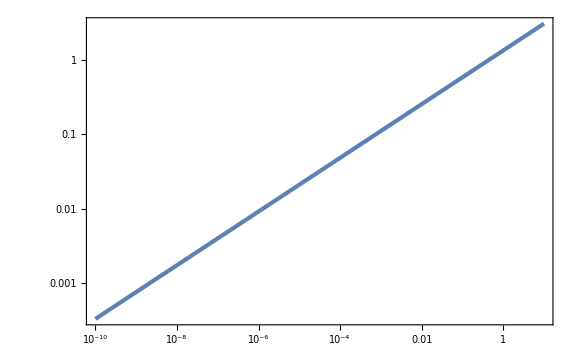

```mathematica
LogLogPlot[MPBH[νth+dν]/Mk0/.params,{dν,10^-10,10}]
```

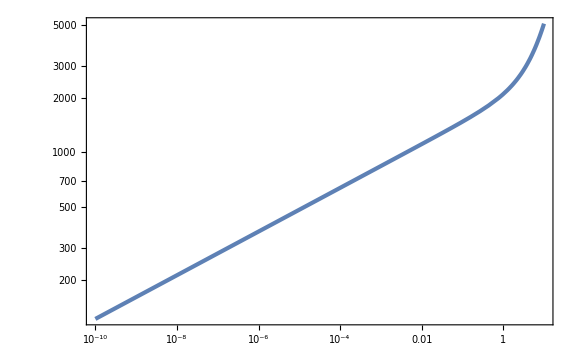

```mathematica
LogLogPlot[Cν[νth+dν]^-1/.params,{dν,10^-10,10}]
```

```mathematica
Cν[νth+10^-10]^-1/.params
Cν[νth+10^-8]^-1/.params
Cν[νth+10^-6]^-1/.params
Cν[νth+10^-4]^-1/.params
Cν[νth+10^-2]^-1/.params
Cν[νth+1]^-1/.params
Cν[νth+10]^-1/.params
```

121.567

211.259

367.126

637.997

1109.63

2090.61

5097.42

```mathematica
Ph[0]
```

0.

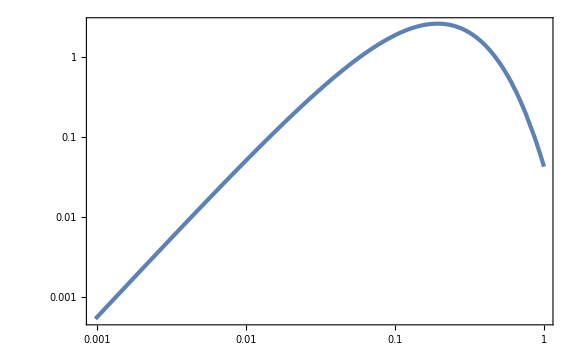

```mathematica
LogLogPlot[Ph[h],{h,0,1}]
```

```mathematica
Ph[0.001]
Ph[0.01]
Ph[0.1]
Ph[1]
```

0.000565916

0.0509213

1.86685

0.0428393

```mathematica
Na[ν_]:=NIntegrate[Ph[h]/.params,{h,0,Cν[ν]^-1/.params},MinRecursion->4,WorkingPrecision->30]
```

```mathematica
Na[νth+10]
```

NIntegrate::precw: The precision of the argument function (563 ⅇ^(8-12 h+2.5 h^1.5-3.2 (1500+h^16)^(1/8)) h^2) is less than WorkingPrecision (30.).

0.999908755887253228668350405841

```mathematica
NaList=Table[{νth+10^dlogν/.params//N,Na[νth+10^dlogν]/.params},{dlogν,-10,1,10^-1}];//AbsoluteTiming
```

NIntegrate::precw: The precision of the argument function (563 ⅇ^(8-12 h+2.5 h^1.5-3.2 (1500+h^16)^(1/8)) h^2) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{3.96167,Null}

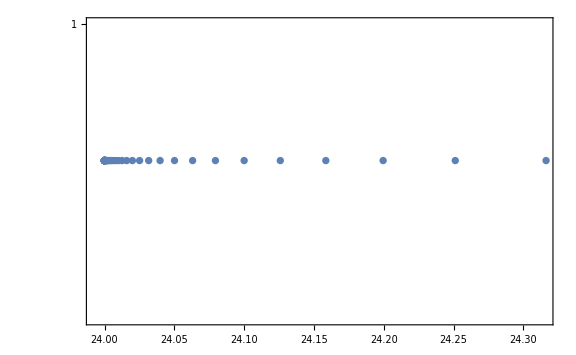

```mathematica
ListLogPlot[NaList,Joined->False]
```

```mathematica
Naint[ν_]=Interpolation[NaList][ν];
```

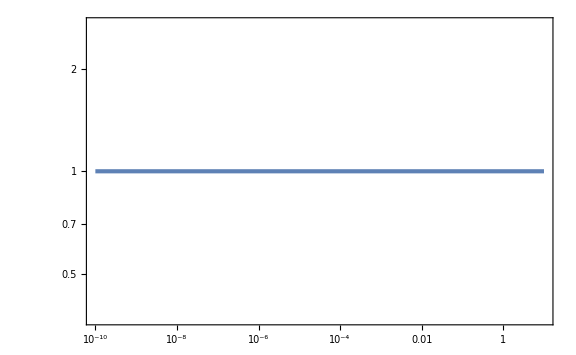

```mathematica
LogLogPlot[Naint[νth+dν]/.params,{dν,10^-10,10},PlotRange->Full]
```

```mathematica
Pa[a_,ν_]=(Cν[ν]^-1 Ph[Cν[ν]^-1 a])/Naint[ν];
```

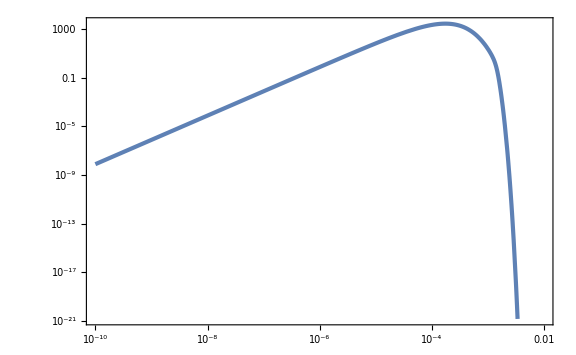

```mathematica
LogLogPlot[Pa[a,νth+10^-2]/.params,{a,10^-10,10^-2}]
```

```mathematica
(Log[1]-Log[10^-8])/0.01
(Log[10]-Log[10^-3])/0.01
(Log[10^-2]-Log[10^-7])/0.01
(1-0.01)/0.01
```

1842.07

921.034

1151.29

99.

```mathematica
920 1150 99
```

104742000

```mathematica
9 12 10
```

1080

```mathematica
Pa[10^-10,νth+10^-2]/.params
Pa[10^-8,νth+10^-2]/.params
Pa[10^-6,νth+10^-2]/.params
Pa[10^-4,νth+10^-2]/.params
Pa[10^-2,νth+10^-2]/.params
```

7.82527×10^-9

0.0000782424

0.772249

2266.45

3.53726×10^-178

```mathematica
NIntegrate[Pa[a,νth+10^1]/.params,{a,0,1},MinRecursion->4]
```

1.

```mathematica
LL[a1_,a2_,χ_,q_]=Min[a1,(1+q)χ+q a2]+Min[a1,q a2-(1+q)χ];
Pν[ν_]=Sqrt[2/π] Erfc[νth/Sqrt[2]]^-1 Exp[-ν^2/2];
```

```mathematica
LL[0.5,0.5,10^-3,0.5]
```

0.5

```mathematica
Integrate[Pν[ν],{ν,νth,∞}]
```

1

```mathematica
Clear[Pintegrand]
```

```mathematica
Pintegrand[calM_,χ_,q_,loga1_,loga2_]:=(LL[E^loga1,E^loga2,χ,q]Pa[E^loga1,νPBH[M1Mq[calM,q]]/.params]Pν[νPBH[M1Mq[calM,q]]/.params]Pa[E^loga2,νPBH[M2Mq[calM,q]]/.params]Pν[νPBH[M2Mq[calM,q]]/.params]/.params)/;(LL[E^loga1,E^loga2,χ,q]>0)
Pintegrand[calM_,χ_,q_,loga1_,loga2_]:=0/;!(LL[E^loga1,E^loga2,χ,q]>0)
```

```mathematica
Pintegrand[1,10^-3,0.5,Log[0.5],Log[0.5]]
```

General::munfl: Exp[-6.6833×10^6] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Clear[PcalMqχ]
PcalMqχ[calM_,q_,χ_]:=(1+q)/(4 q^2 β^2 σ0^2)(((1+q)^(2/5)calM^2)/(q^(1/5)KK^2 Mk0^2))^(1/β)NIntegrate[Pintegrand[calM,χ,q,loga1,loga2],{loga1,-10Log[10],0},{loga2,-10Log[10],0},WorkingPrecision->30,MinRecursion->4]/.params
```

```mathematica
PcalMqχ[1,0.5,10^-3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.0694897251412810538943480991065279662549041134838234158988376353691051734428773×10^-33 and 1.861365592650298138595115983437095628457746396053726463074576212206271679817363×10^-39 for the integral and error estimates.

5.87146×10^-33

```mathematica
Log10PcalMqχList=Map[{#[[1]],#[[2]],#[[3]],Log10[Max[#[[4]],10^-30]]}&,Sort[Import["c++/PcalMqchi.dat"]]];
Log10PcalMqχListK=Map[{#[[1]],#[[2]],#[[3]],Log10[Max[#[[4]],10^-30]]}&,Sort[Import["c++/PcalMqchi_Koga.dat"]]];
```

```mathematica
Log10PcalMqχint[calM_,q_,χ_]=Interpolation[Log10PcalMqχList,InterpolationOrder->1][calM,q,χ];
Log10PcalMqχintK[calM_,q_,χ_]=Interpolation[Log10PcalMqχListK,InterpolationOrder->1][calM,q,χ];
```

```mathematica
Log10PcalMqχint[0.5,0.4,10^-3]
Log10PcalMqχintK[0.5,0.4,10^-3]
```

-11.3558

-11.3559

```mathematica
Log10PcalMqχint[10^-0.7,0.5,10^-4.1]
Log10PcalMqχintK[10^-0.7,0.5,10^-4.1]
```

-1.20866

-1.2081

```mathematica
Manipulate[ContourPlot[Log10PcalMqχint[10^logM,q,10^logχ],{logχ,-7,-2},{q,0.01,1},Contours->Function[{min,max},Range[-15,max,1]],PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10"P["lnℳ",q,"lnχ"],Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",logM}]}}],{logM,-3,1,0.1}]
```

InterpolatingFunction::dmval: Input value {0.0630957,0.0100707,1.00082×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
lnM=-0.5;
ContourPlot[Log10PcalMqχint[10^lnM,q,10^logχ],{logχ,-7,-2},{q,0.01,1},Contours->Function[{min,max},Range[-15,max-2,1]],PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10"Subscript[P, Tada]["lnℳ",q,"lnχ"],Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",lnM}]}}]
ContourPlot[Log10PcalMqχintK[10^lnM,q,10^logχ],{logχ,-7,-2},{q,0.01,1},Contours->Function[{min,max},Range[-15,max-2,1]],PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10"Subscript[P, Koga]["lnℳ",q,"lnχ"],Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",lnM}]}}]
```

-Graphics-

-Graphics-

```mathematica
Log10PcalMqχintK[10^-3,0.01,10^-7]
Log10PcalMqχint[10^-3,0.01,10^-7]
```

-14.5441

-14.5441

```mathematica
Log10[3.23 10^-14]
Log10[2.86 10^-15]
```

-13.4908

-14.5436

```mathematica
lnM=-3;
ContourPlot[10^(Log10PcalMqχintK[10^lnM,q,10^logχ]-Log10PcalMqχint[10^lnM,q,10^logχ]),{logχ,-7,-2},{q,0.01,1},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["P_Koga/P_Tada",Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",lnM}]}}]
```

-Graphics-

```mathematica
lnM=-2;
ContourPlot[10^(Log10PcalMqχintK[10^lnM,q,10^logχ]-Log10PcalMqχint[10^lnM,q,10^logχ]),{logχ,-7,-2},{q,0.01,1},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["P_Koga/P_Tada",Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",lnM}]}}]
```

-Graphics-

```mathematica
lnM=-1;
ContourPlot[10^(Log10PcalMqχintK[10^lnM,q,10^logχ]-Log10PcalMqχint[10^lnM,q,10^logχ]),{logχ,-7,-2},{q,0.01,1},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["P_Koga/P_Tada",Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",lnM}]}}]
```

-Graphics-

```mathematica
lnM=0;
ContourPlot[10^(Log10PcalMqχintK[10^lnM,q,10^logχ]-Log10PcalMqχint[10^lnM,q,10^logχ]),{logχ,-7,-2},{q,0.01,1},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["P_Koga/P_Tada",Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",lnM}]}}]
```

-Graphics-

```mathematica
Table[Export["KogaTada"<>ToString[lnM]<>".pdf",ContourPlot[10^(Log10PcalMqχintK[10^lnM,q,10^logχ]-Log10PcalMqχint[10^lnM,q,10^logχ]),{logχ,-7,-2},{q,0.01,1},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["P_Koga/P_Tada",Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",lnM}]}}]],{lnM,-3,0}];
```

```mathematica
FigPcalMqχList=Table[ContourPlot[Log10PcalMqχint[10^logM,q,10^logχ],{logχ,-7,-2},{q,0.01,1},Contours->Function[{min,max},Range[-15,max-1,1]],PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10"P["lnℳ",q,"lnχ"],Right,Rotate[#,-90Degree]&]],FrameLabel->{{q,None},{"log_10χ",Row[{"log_10ℳ = ",logM//N}]}}],{logM,-3,3 10^-2,10^-2}];//AbsoluteTiming
```

{926.169,Null}

```mathematica
Export["PcalMqχ.gif",FigPcalMqχList];//AbsoluteTiming
```

{184.352,Null}

```mathematica
Pχq[χ_,q_]:=NIntegrate[Pintegrand[χ,q,log10a1,log10a2,log10δν1],{log10a1,-7,0},{log10a2,-7,0},{log10δν1,-7,1},Method->"AdaptiveMonteCarlo"]
```

```mathematica
Pχq[0,1]//AbsoluteTiming
```

{1.40455,179.979}

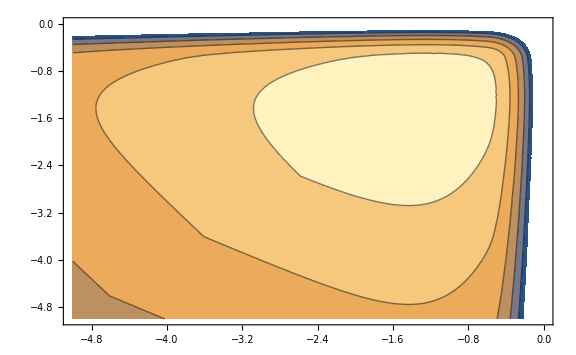

```mathematica
ContourPlot[Log10[Pintegrand[0,1,log10a1,log10a2,-5]],{log10a1,-5,0},{log10a2,-5,0}]
```

```mathematica
P0qList=ParallelTable[{i/10,Pχq[0,i/10]//Quiet},{i,1,10}];//AbsoluteTiming
```

{31.0494,Null}

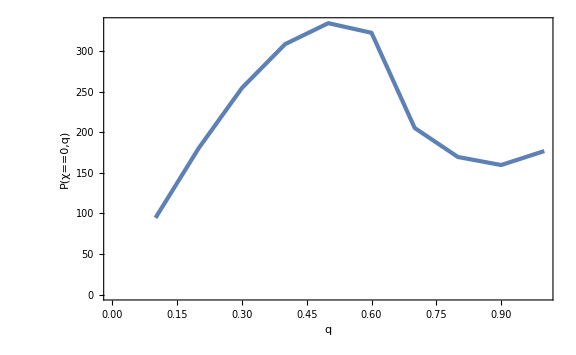

```mathematica
ListPlot[P0qList,FrameLabel->{q,P[χ==0,q]}]
```

```mathematica
PχqList=Flatten[ParallelTable[{logχ,q,Log10[Pχq[10^logχ,q]//Quiet]},{logχ,-7,0,1/50},{q,0,1,1/50}],1];//AbsoluteTiming
```

{56630.4,Null}

```mathematica
Export["Pchiq.dat",PχqList];
```

```mathematica
2363 25/86400//N
```

0.683738

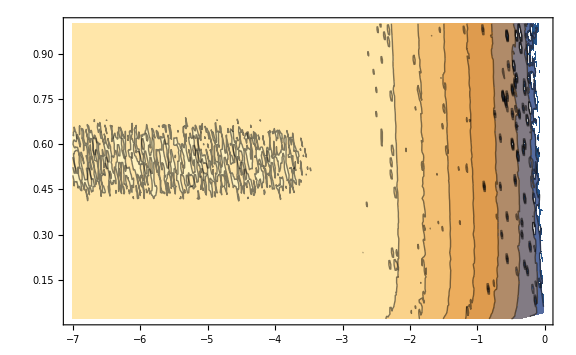

```mathematica
ListContourPlot[PχqList]
```

```mathematica
Pχqint[χ_,q_]=10^(Interpolation[PχqList,InterpolationOrder->1][Log10[χ],q]);
```

```mathematica
FigPχqContour=ContourPlot[Log10[Log[10] 10^logχ Pχqint[10^logχ,q]],{logχ,-7,0},{q,0,1},Contours->Table[i,{i,-15,0}],FrameLabel->{"log_10"χ,q},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10"P["log_10"χ,q],Right,Rotate[#,-90Degree]&]]]
```

-Graphics-

```mathematica
Export["PchiqContour.pdf",FigPχqContour];
```

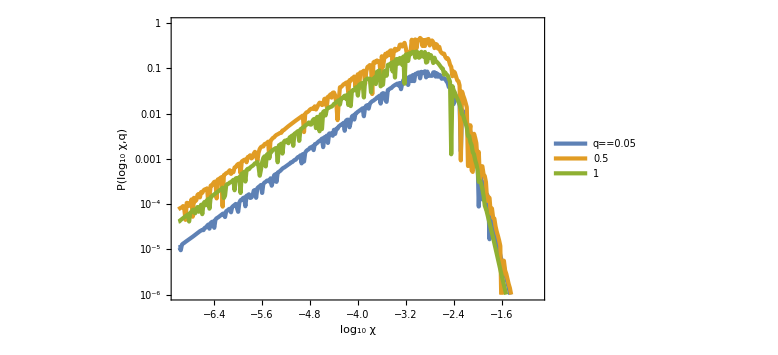

```mathematica
LogPlot[{Log[10] 10^logχ Pχqint[10^logχ,0.05],Log[10] 10^logχ Pχqint[10^logχ,0.5],Log[10] 10^logχ Pχqint[10^logχ,1]},{logχ,-7,-1},PlotRange->{10^-6,1},FrameLabel->{"log_10"χ,P["log_10"χ,q]},PlotLegends->Placed[LineLegend[{q==0.05,0.5,1},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendLayout->"Row"],{0.4,0.15}]]
```

```mathematica
NIntegrate[Log[10] 10^logχ Pχqint[10^logχ,q],{logχ,-7,0},{q,1/50,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.305851+5.39397×10^-17 ⅈ and 0.000034758 for the integral and error estimates.

0.305851